## Machine Learning

```mathematica
Classify["Language","测试"]
```

Chinese

```mathematica
Classify["NameGender","Kevin"]
```

Male

```mathematica
imag=-Graphics-
```

```mathematica
ImageIdentify[imag]
```

Ash's Pikachu

```mathematica
imag=-Graphics-
```

```mathematica
ImageIdentify[imag]
```

Batman

```mathematica
imag=-Graphics-
```

-Graphics-

```mathematica
ImageIdentify[imag]
```

domestic cat

```mathematica
c=Classify[{1->"A",2->"A",3->"B",4->"B"}]
```

ClassifierFunction[…]

```mathematica
c[2.1,"Probabilities"]
```

<|A→0.500071,B→0.499929|>

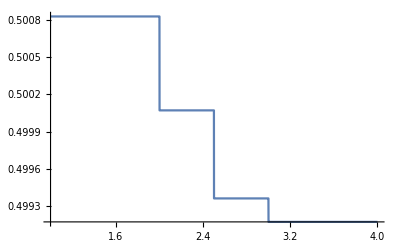

```mathematica
Plot[c[x,"Probabilities"][[1]],{x,1,4}]
```

```mathematica
p=Predict[{1->1.5,2->2.4,3->3.4,4->4.5}]
```

PredictorFunction[…]

```mathematica
p[2.5]
```

2.95

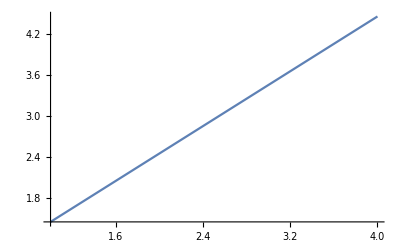

```mathematica
Plot[p[x],{x,1,4}]
```

```mathematica
resource=ResourceObject["MNIST"]
```

ResourceObject[…]

```mathematica
trainingData=ResourceData[resource,"TrainingData"];
testData=ResourceData[resource,"TestData"];
```

```mathematica
Length[trainingData]
```

60000

```mathematica
RandomSample[trainingData,5]
```

{-Graphics-→1,-Graphics-→9,-Graphics-→0,-Graphics-→2,-Graphics-→3}

```mathematica
lenet=NetChain[{
ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[50,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[10],
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",Range[0,9]}],
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

| input | image
3-tensor (size: ××12828)
1 | convolution | 3-tensor (size: ××202424)
2 | ReLU | 3-tensor (size: ××202424)
3 | pooling | 3-tensor (size: ××201212)
4 | convolution | 3-tensor (size: ××5088)
5 | ReLU | 3-tensor (size: ××5088)
6 | pooling | 3-tensor (size: ××5044)
7 | flatten | vector (size: ××800)
8 | linear | vector (size: ××500)
9 | ReLU | vector (size: ××500)
10 | linear | vector (size: ××10)
11 | softmax | vector (size: ××10)
 | output | class

```mathematica
trained=NetTrain[lenet,trainingData,ValidationSet->testData,MaxTrainingRounds->4]
```

| input | image
3-tensor (size: ××12828)
1 | convolution | 3-tensor (size: ××202424)
2 | ReLU | 3-tensor (size: ××202424)
3 | pooling | 3-tensor (size: ××201212)
4 | convolution | 3-tensor (size: ××5088)
5 | ReLU | 3-tensor (size: ××5088)
6 | pooling | 3-tensor (size: ××5044)
7 | flatten | vector (size: ××800)
8 | linear | vector (size: ××500)
9 | ReLU | vector (size: ××500)
10 | linear | vector (size: ××10)
11 | softmax | vector (size: ××10)
 | output | class

```mathematica
RandomSample[testData,5]
```

{-Graphics-→9,-Graphics-→0,-Graphics-→8,-Graphics-→2,-Graphics-→3}

```mathematica
trained[-Graphics-]
```

9

```mathematica
trained[-Graphics-]
```

2